# 1D linear stability analysis (LSA) wavelength and period calculation for the switch model

Parameters transformed to the 1+1D geometry by bulk-boundary ratio of a cylinder of radius 0.5μm

```mathematica
paramsSwitch={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3*4,
kdD->0.0015*4,
kdEr->1.5*4,
kdEl->10^-5*4,
kde->1,
λ->5,
μ->20
};
```

## Setup

Setup the reaction terms for the 1+1D switch model

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
-μ cEr+kde mde-kdEr md cEr,
μ cEr-kdEl md cEl,
(kD+kdD md)cDT-kdEr md cEr-kdEl md cEl,
kdEr md cEr+kdEl md cEl-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,5,6}]]
Simplify[Total@f[[{3,4,6}]]]
```

0

0

## Homogeneous fixed point

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cEr+cEl+mde}/.params,{cDD,cDT,cEr,cEl,md,mde}];
Select[{cDD,cDT,cEr,cEl,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cEr,
-DE q^2 cEl ,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cEr,cEl,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cEr,cEl,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS
}
];
```

## LSA

### Quantifying instability

#### Slices at constant rhoD and rhoE through the phase diagram

```mathematica
Monitor[sweepEslice=Table[
{
rho,
testInstab[Join[{rhoD->1500/4,rhoE->rho/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->2000,"maxQ"->2]
},{rho,10^Range[2,4.5,0.01]}];,rho]
```

```mathematica
analysisEslice=Block[{maxList},
If[#[[2,1]]>0,
maxList=SortBy[#[[2,2]],Function[x,Re[x[[2,-1]]]]];
{#[[1]],2Pi/maxList[[-1,1]],2Pi/Re@maxList[[-1,2,-1]],Im@maxList[[-1,2,-1]]},{#[[1]],0,0,0}]]&/@sweepEslice;
```

```mathematica
Monitor[sweepDslice=Table[
{
rho,
testInstab[Join[{rhoD->rho/4,rhoE->13500/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->2000,"maxQ"->2]
},{rho,10^Range[2,4.5,0.01]}];,rho]
```

```mathematica
analysisDslice=Block[{maxList},
If[#[[2,1]]>0,
maxList=SortBy[#[[2,2]],Function[x,Re[x[[2,-1]]]]];
{#[[1]],2Pi/maxList[[-1,1]],2Pi/Re@maxList[[-1,2,-1]],Im@maxList[[-1,2,-1]]},{#[[1]],0,0,0}]]&/@sweepDslice;
```

#### Wavelengths

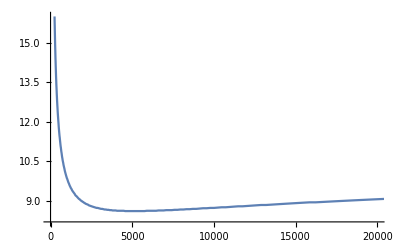

```mathematica
ListLinePlot[{#[[1]],#[[2]]}&/@Select[analysisEslice,#[[2]]>0&],PlotRange->{{0,20000},Automatic}]
```

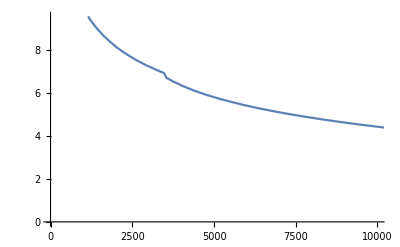

```mathematica
ListLinePlot[{#[[1]],#[[2]]}&/@Select[analysisDslice,#[[2]]>0&],PlotRange->{{0,10000},Automatic}]
```

Reason for discontinuity are the different branches of the dispersion relation:

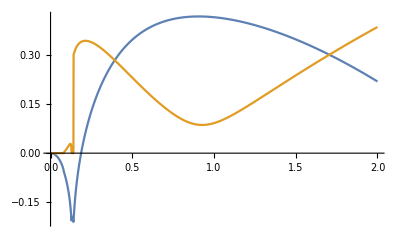

```mathematica
ListLinePlot[{{#[[1]],Re@#[[2,-1]]}&/@sweepDslice[[155,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@sweepDslice[[155,2,2]]
}]
```

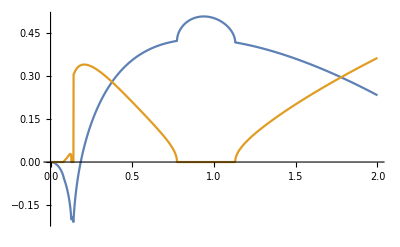

```mathematica
ListLinePlot[{{#[[1]],Re@#[[2,-1]]}&/@sweepDslice[[156,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@sweepDslice[[156,2,2]]
}]
```

#### Oscillation periods

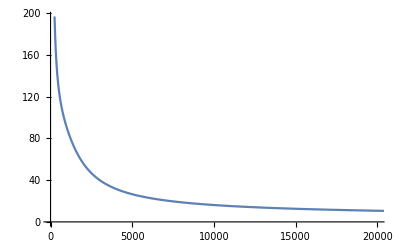

```mathematica
ListLinePlot[{#[[1]],2Pi/#[[4]]}&/@Select[analysisEslice,#[[2]]>0&],PlotRange->{{0,20000},Automatic}]
```

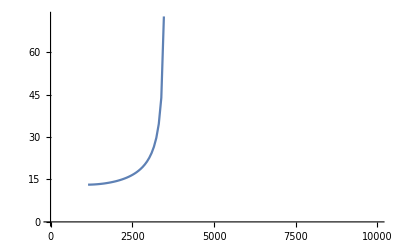

```mathematica
ListLinePlot[{#[[1]],2Pi/#[[4]]}&/@Select[analysisDslice,(#[[2]]>0&&Abs[#[[4]]]>0)&],PlotRange->{{0,10000},All}]
```